#### Blatt 3

Jonas Neundorf, Jan Skottke

Definiere eine Funktion, die das System einen Schritt weiterentwickelt. Alle Impulse sind auf den Anfangsimpuls p_0 normiert.

```mathematica
schritt[{x_, px_, z_, pz_}] := Module[{x2, px2, z2},
  deltaZ = 0.1;
  k = .001;(*1.602*10^-19*g/p0;*)
x2:=x+px*deltaZ;
px2:=px-k*x2*pz*deltaZ;
z2:=z+pz*deltaZ;
Return[{x2,z2,px2,pz}](*Keine B-Feld Komponente in z-Richtung, daher keine Impulsänderung in z-Richtung*)
]
```

Um nun den Verlauf zu simulieren, muss eine Anfangsverteilung aufgestellt werden. z kann beliebig gewählt werden, p_z ist aufgrund der Normierung gleich 1. x und p_x sollten einer Normalverteilung um 0 mit kleiner Standardabweichung folgen. Es sei nun, um ein Gefühl für die Größen zu kriegen, p_x=0.01, x=0.

```mathematica
NestList[schritt,{x,px,z,pz},10]/.{x->-1,px->0.01,z->0,pz->1}
```

{{-1,0.01,0,1},{-0.999,0.1,0.0100999,1},{-0.989,0.1101,0.100099,1},{-0.97799,0.200099,0.110198,1},{-0.95798,0.210198,0.200195,1},{-0.93696,0.300195,0.210291,1},{-0.906941,0.310291,0.300285,1},{-0.875912,0.400285,0.310379,1},{-0.835883,0.410379,0.400369,1},{-0.794845,0.500369,0.410458,1},{-0.744808,0.510458,0.500443,1}}

Erzeuge ein Teilchen

```mathematica
teilchen := {RandomReal[NormalDistribution[0,1]],RandomReal[NormalDistribution[0,1]],0,1}
```

```mathematica
teilchen
```

{0.764235,-1.59266,0,1}

Definiere eine pure function um NestList auf Teilchen anwenden zu können

```mathematica
nextstep = Function[{x},schritt[{x[[1]],x[[2]],x[[3]],x[[4]]}]]
```

Function[{x},schritt[{x⟦1⟧,x⟦2⟧,x⟦3⟧,x⟦4⟧}]]

```mathematica
nextstep[teilchen]
```

{-0.880416,0.1,0.787348,1}

Berechne die nächsten 10 Schritte eines Teilchens.

```mathematica
NestList[nextstep,teilchen,10]
```

{{0.0675112,-0.662002,0,1},{0.00131098,0.1,-0.662002,1},{0.011311,-0.562002,0.0999989,1},{-0.0448893,0.199999,-0.561998,1},{-0.0248894,-0.461998,0.200001,1},{-0.0710892,0.300001,-0.461991,1},{-0.041089,-0.361991,0.300005,1},{-0.0772881,0.400005,-0.361983,1},{-0.0372876,-0.261983,0.400009,1},{-0.0634859,0.500009,-0.261977,1},{-0.013485,-0.161977,0.500011,1}}

Nun versuche eine Liste von Teilchen auszuwerten. Zunächst wird eine Liste von 100 Teilchen erzeugt

```mathematica
lteilchen :=Table[{RandomReal[NormalDistribution[0,1]],RandomReal[NormalDistribution[0,1]],0,1},100]
```

Nun definieren wir uns eine pure function, die die Funktion schritt auf eine Liste anwendet.

```mathematica
nextsteplist = Function[{x},Map[schritt,x]]
```

Function[{x},schritt/@x]

Berechne die nächsten 100 Schritte für jedes Teilchen

```mathematica
data=NestList[nextsteplist,lteilchen,100];
```

Plotte x gegen p_x für die gesamte Flugzeit für das 1. Teilchen

```mathematica
test = data[[All, 1,1;;2]];
```

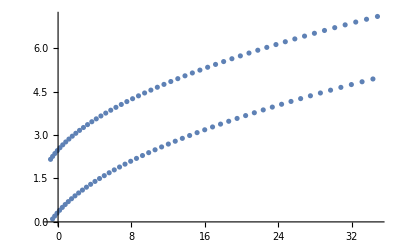

```mathematica
ListPlot[test]
```

Plotte z gegen p_z für die gesamte Flugzeit für das 1. Teilchen

```mathematica
test2 := data[[All, 1,3;;4]];
```

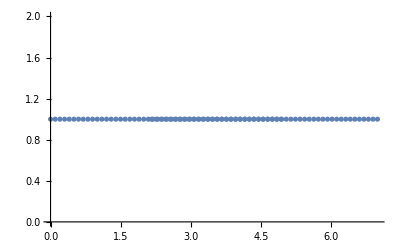

```mathematica
ListPlot[test2]
```

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points {1,y_1},{2,y_2},…. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{data_1,data_2,…}] plots data from all the data_i.
ListPlot[{…,w[data_i,…],…}] plots data_i with features defined by the symbolic wrapper w.